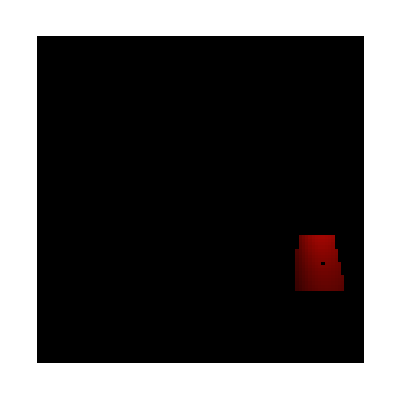

{True,{0.0617521,0.00239058,0.000640753},{0.061752,0.002391,0.000641}}

<|total→256,ok→255,fail→1,black→49,failedPixel→{87,69}|>

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtPath`"];
Needs["pbrtPathLog`"];
SetDirectory[NotebookDirectory[]];

ClearAll[sppmPixelArray,sppmRenderPixelEntry,getSppmPixelOffset,getSppmPixel,
	sppmIntegratorRender,sppmGenVisPoints,sppmGenVisPointsBounce,updateSppmPixel,
	sppmTracePhotonsBounce,sppmComputePixelRadiance,sppmIntegratorRenderIteration,
	sppmImgTable,sppmImgColorMul,getSppmImageTable,updateSppmImageTable,
	sppmGetTestPixelColor,sppmValidateSinglePixel,sppmValidateTilePixels];

sppmPixelArray=<||>;
sppmImgColorMul=1;

sppmRenderPixelEntry[pixel_,scene_,nIteration_,maxDepth_]:=Module[
{tileMin,tileMax},
tileMin={pixel[[1]],pixel[[2]]};
tileMax={pixel[[1]],pixel[[2]]};

sppmIntegratorRender[tileMin,tileMax,scene,nIteration,maxDepth]
];

(*SPPMIntegrator::Render*)
sppmIntegratorRender[tileMin_,tileMax_,scene_,nIteration_,maxDepth_]:=Module[
{nPixels,resx,resy,iter,i,tmp},
resx=scene["resx"];
resy=scene["resy"];

(*init SPPM pixels*)
nPixels=resx*resy;
For[i=0,i<nPixels,i++,
sppmPixelArray[ToString@i]=<|"index"->i,"radius"->0,"ld"->{0,0,0},"l"->{0,0,0},
"vp_p"->{0,0,0},"vp_wo"->{0,0,0},"vp_bsdf"-><||>,"vp_beta"->{1,1,1},
"phi"->{},"m"->0,"n"->0,"tau"->{0,0,0}|>
];

(*init image table*)
sppmImgTable=Table[1,resx,resy];
For[i=1,i≤resx,i++,
For[j=1,j≤resy,j++,
 sppmImgTable[[i]][[j]]=RGBColor[0,0,0];
]
];

(*sppmIntegratorRenderIteration*)
For[iter=0,iter<nIteration,iter++,
tmp=sppmIntegratorRenderIteration[iter,tileMin,tileMax,scene,nIteration,maxDepth];
];

tmp
];

(*sppmIntegratorRenderIteration*)
sppmIntegratorRenderIteration[iter_,tileMin_,tileMax_,scene_,
nIteration_,maxDepth_]:=Module[
{i,j,pixel,endLabel},

(*Part_1: sppmGenVisPoints*)
For[i=tileMin[[1]],i≤tileMax[[1]],i++,
For[j=tileMin[[2]],j<=tileMax[[2]],j++,
pixel={i,j};
sppmGenVisPoints[pixel,scene,maxDepth];
];
];

(*Part_2:sppmTracePhotons*)
(*sppmTracePhotons[pixel,scene,maxDepth];*)

(*Part_3:sppmUpdatePixelValues*)

(*Part_4:sppmComputePixelRadiance*)
If[iter+1!=nIteration,Goto[endLabel]];
For[i=tileMin[[1]],i≤tileMax[[1]],i++,
For[j=tileMin[[2]],j<=tileMax[[2]],j++,
pixel={i,j};
sppmComputePixelRadiance[pixel,scene,nIteration];
];
];

Label[endLabel];
1
];

(*Part_1: sppmGenVisPoints*)
sppmGenVisPoints[pixel_,scene_,maxDepth_]:=Module[
{camRayo,camRayd,beta,visPts,sppmPixel},
sppmPixel=getSppmPixel[pixel,scene];

camRayo=gAssocData[scene,"eyePt"];
camRayd=pbrtRayDifferential[pixel,scene];

(*Part_1:sppmGenVisPointsBounce*)
beta={1,1,1};
visPts=sppmGenVisPointsBounce[pixel,{camRayo,camRayd},beta,scene,0];

visPts
];

(*Part_1:sppmGenVisPointsBounce*)
sppmGenVisPointsBounce[pixel_,ray_,beta_,scene_,bounceIndex_]:=Module[
{rayo,rayd,l,ld,isect1,isectWithBsdf,wo,tmpL,endLabel},
rayo=ray[[1]];
rayd=ray[[2]];
l={0,0,0};
ld={0,0,0};

isect1=pbrtSceneIntersect[ray,scene];
If[ToString@isect1=="NaN",Goto[endLabel]];

(*Compute BSDF at SPPM camera ray intersection*)
isectWithBsdf=pbrtComputeScatteringFunctions[isect1];
(*Accumulate light contributions for ray with no intersection*)
If[ToString@isectWithBsdf=="NaN",
updateSppmPixel[pixel,scene,"ld",{0,0,0}];
Goto[endLabel]];

(*Accumulate direct illumination at SPPM camera ray intersection*)
wo=-rayd;
tmpL=If[bounceIndex>0,{0,0,0},pbrtSurfaceInteractionLe[isect1,wo]];
ld+=beta*tmpL;
tmpL=pbrtUniformSampleOneLight[isectWithBsdf,scene];
ld+=beta*tmpL;

updateSppmPixel[pixel,scene,"ld",ld];
updateSppmPixel[pixel,scene,"vp_p",isectWithBsdf["p"]];
updateSppmPixel[pixel,scene,"vp_wo",wo];
updateSppmPixel[pixel,scene,"vp_bsdf",isectWithBsdf["bsdf"]];
updateSppmPixel[pixel,scene,"vp_beta",beta];

Label[endLabel];

];

(*Part_2:sppmTracePhotons*)
sppmTracePhotons[pixel_,scene_,maxDepth_]:=Module[
{uLight0,uLight1,light,lightPdf,
lightLe,le,photonRay,lightNormal,pdfPos,pdfDir,
beta,endLabel},
uLight0=pbrtGet2D[];
uLight1=pbrtGet2D[];

light=scene["lights"][[1]];
lightPdf=1;

lightLe=pbrtLightSampleLe[light,uLight0,uLight1];
le=lightLe["l"];
photonRay=lightLe["photonRay"];
lightNormal=lightLe["lightNormal"];
pdfPos=lightLe["pdfPos"];
pdfDir=lightLe["pdfDir"];

If[pdfPos==0||pdfDir==0||pbrtIsBlack[le],Goto[endLabel]];
beta=(Abs@Dot[lightNormal,photonRay[[2]]]*le)/(lightPdf * pdfPos * pdfDir);
If[pbrtIsBlack[beta],Goto[endLabel]];

(*Part_2:sppmTracePhotonsBounce*)
sppmTracePhotonsBounce[photonRay,beta,scene,0];

Label[endLabel];
lightLe
];

(*Part_4:sppmComputePixelRadiance*)
sppmComputePixelRadiance[pixel_,scene_,nIteration_]:=Module[
{sppmPixel,iter,ld,l},
sppmPixel=getSppmPixel[pixel,scene];

Assert[nIteration==1];
iter=0;
ld=sppmPixel["ld"];
l=ld/(iter+1);
updateSppmPixel[pixel,scene,"l",l];

updateSppmImageTable[pixel,l];
];

(*Part_2:sppmTracePhotonsBounce*)
sppmTracePhotonsBounce[photonRay_,beta_,scene_,bounceIndex_]:=Module[
{},

1
];

getSppmImageTable[pixel_]:=Module[
{},

sppmImgTable[[pixel[[2]]+1]][[pixel[[1]]+1]]
];

updateSppmImageTable[pixel_,l_]:=Module[
{rgbColor},

rgbColor=RGBColor[{l[[1]],l[[2]],l[[3]]} * sppmImgColorMul];
sppmImgTable[[pixel[[2]]+1]][[pixel[[1]]+1]]=rgbColor;
];

getSppmPixelOffset[pixel_,scene_]:=Module[
{pixelOffset},

pixelOffset=pixel[[1]] + pixel[[2]]*scene["resx"];
pixelOffset
];

getSppmPixel[pixel_,scene_]:=Module[
{pixelOffset,sppmPixel},

pixelOffset=getSppmPixelOffset[pixel,scene];
sppmPixel=sppmPixelArray[ToString@pixelOffset];

sppmPixel
];

updateSppmPixel[pixel_,scene_,key_,value_]:=Module[
{pixelOffset,sppmPixel},

pixelOffset=getSppmPixelOffset[pixel,scene];
sppmPixelArray[ToString@pixelOffset][key]=value
];

sppmGetTestPixelColor[pixel_,scene_,testData_]:=Module[
	{resx,resy,idx,x,y,z},
	resx=gAssocData[scene,"resx"];
	resy=gAssocData[scene,"resy"];
	
	idx=(pixel[[1]]+pixel[[2]]*resx)*3;
	x=testData[[idx+1]];
	y=testData[[idx+2]];
	z=testData[[idx+3]];
	
	{x,y,z}
];

sppmValidateSinglePixel[pixel_,scene_,testData_]:=Module[
{sppmPixel,pixelA,pixelB,test},

sppmRenderPixelEntry[pixel,scene,1,1];
sppmPixel=getSppmPixel[pixel,scene];
pixelA=sppmPixel["l"];pixelB=sppmGetTestPixelColor[pixel,scene,testData];

test=If[gColorEquals[pixelA,pixelB],True,False];
{test,pixelA,pixelB}
];

sppmValidateTilePixels[tileMin_,tileMax_,scene_,testData_]:=Module[
	{i,j,ret,testOK,renderedPixel,testPixel},

	(*debugData={};*)
	ret=<|"total"->0,"ok"->0,"fail"->0,"black"->0|>;
	For[i=tileMin[[1]],i<tileMax[[1]],i++,
		For[j=tileMin[[2]],j<tileMax[[2]],j++,
			ret["total"]+=1;
			{testOK,renderedPixel,testPixel}=sppmValidateSinglePixel[{i,j},scene,testData];
			If[testOK,ret["ok"]+=1,ret["fail"]+=1];
			If[!testOK,ret["failedPixel"]={i,j}];
			If[pbrtIsBlack[renderedPixel],ret["black"]+=1];
			(*If[!pbrtIsBlack[renderedColor],Print[{i,j,}]]*)
			(*AppendTo[debugData,testOK];*)
		];
	];

	ret
	(*debugData*)
];


ClearAll[scene,l1,debugPixel,sppmPixel];
sppmImgColorMul=10;
scene=pbrtLoadScene["cornell-tiny.scene"];
debugPixel={85,61};
(*debugPixel={51,12};*)
(*debugPixel={87,69};*)
(*debugPixel={78,76};
l1=sppmRenderPixelEntry[debugPixel,scene,1,1];
sppmPixel=getSppmPixel[debugPixel,scene];
sppmPixel;*)

sppmIntegratorRender[{77,61},{93,77},scene,1,1];
(*sppmIntegratorRender[{86,68},{88,70},scene,1,1];*)
ArrayPlot[sppmImgTable]

testData=ToExpression[Import["cornell-tiny.pixels"]];
sppmValidateSinglePixel[debugPixel,scene,testData]
sppmValidateTilePixels[{77,61},{93,77},scene,testData]
```